## Trait-Based Model

This model examines how the initial distribution of traits in a microbial population impacts diversity in a chemostat as dilution rate increases.  Two scenarios are examined, one where the trait governing bacteria specific growth rate, ϵ_i  is uniformly distributed, such that there are as many bacteria that have a specific growth rate near the upper growth rate limit as for any other specific growth rate. The other scenario examines our hypothesis that as you approach the upper specific growth rate limit for bacteria, there are many fewer ASVs capable of growing at that boundary. We randomly select ϵ_i from a beta probability distribution to explore the second scenario. Experimental details and data the model simulates can be found here http://ecosystems.mbl.edu/MEP-FoodWeb/Experiments/Exp1/index.html
22-Jul-2024
This Version 2 includes a quadratic mortality term weighted by relative ASV abundance for the bacterial balance equation.

## Notebook setup

Set the working directory to where this notebook is saved

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jvallino\OneDrive - Marine Biological Laboratory\Documents\AshelyMegSESpaper\Supplemental\Model

Turn  off  plot  highlighting  as  it  slows  the  front  end  down  when  plots  have  a  lot  of  elements

```mathematica
Charting`$InteractiveHighlighting=False;
SetOptions[Plot,PlotHighlighting->None];
SetOptions[ListPlot,PlotHighlighting->None];
```

Plot  sometimes  needs more recursion than the default, so set it higher here

```mathematica
$RecursionLimit=2000;
```

To  decrease file  size, hold  Alt  then  click  on  an  output  cell, then from the menu select “Cell → Convert To → Bitmap”. (note, Alt+click selects all output cells). Also, graph outputs can be wrapped with Rasterize[], which does the same thing.

## Experimental On-Line Data

Dissolved oxygen, DO (μM), and partial pressure of oxygen in the chemostat gas headspace (%) from MC1 and MC2 during the course of the experiment.

Import Exp1.csv that has the O2, CO2, DO and pH for the two chemostats.  From Exp1.csv, just use the O2 data, as the DO can be obtained from the Exp1_DOpH.csv file, which is of higher resolution because it did not rely on an  A2D converted.  In both cases drop the header from the csv data.

```mathematica
o2Data={Drop[Import["../Data/Exp1.csv"],1]⟦All,{1,2}⟧,Drop[Import["../Data/Exp1.csv"],1]⟦All,{6,7}⟧};
```

```mathematica
Dimensions[o2Data]
```

{2,639,2}

Plot the pO2 data

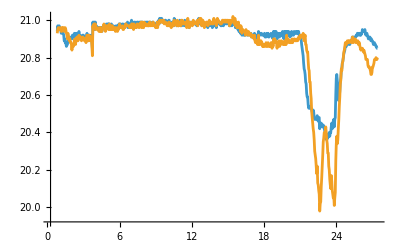

```mathematica
ListLinePlot[o2Data,PlotRange->All]
```

```mathematica
doData={Drop[Import["../Data/Exp1_DOpH.csv"],1]⟦All,{3,4}⟧,Drop[Import["../Data/Exp1_DOpH.csv"],1]⟦All,{7,8}⟧};
```

Now convert mg/L to uM O2

```mathematica
doData={doData⟦1⟧/.{x_,y_}->{x,1000y/32},doData⟦2⟧/.{x_,y_}->{x,1000y/32}};
```

Plot the DO data

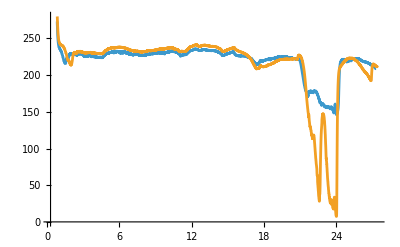

```mathematica
ListLinePlot[doData,PlotRange->All]
```

### Dissolved Oxygen Data for k_L estimation

This data is used to determine the liquid-side oxygen mass transfer velocity, k_L (see below). DO data was collected following sparging of the chemostat with N_2 gas. After sparging with N2, the gas flow was changed to air, and the chemostat headspace was quickly equilibrated with air using a small fan for a short time so that the gas overlying the water would be at atmospheric pressures (i.e., fixed boundary condition). Import the DO data:

```mathematica
o2DataN2=Import["../Data/DO_N2toAir.dat"];
```

Plot the DO observations.

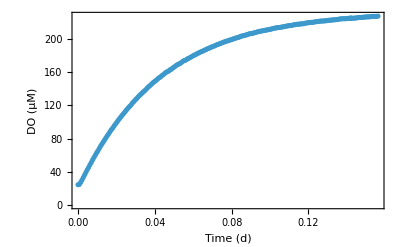

```mathematica
ListPlot[o2DataN2,FrameLabel->{"Time (d)","DO (μM)"},Frame->{{True,False},{True,False}},BaseStyle->{FontSize->15,FontWeight->Bold}]
```

## Estimate k_L a from data for transition from N_2 to Air

### Preliminary model testing (no need to evaluate this subsection)

Simple model for dissolved oxygen, c, and partial pressure, p, in the chemostat based on how the chemostat design.

```mathematica
odes[input_List]:={
c'[t]==(fL(cF-c[t])+kL a(p[t]h-c[t]))/vL,
p'[t]==(fG(pF-p[t])+kL a rGas tK(c[t]-p[t]h))/vG,
c[0]==cF,
p[0]==0
}/.input
```

Henry' s law for oxygen (from http : // satellite.mpic.de/henry/casrn/7782 - 44 - 7)

```mathematica
hO2[tk_]:=0.00131722 ⅇ^(1700(1/tk-1/298.15))10^6
```

Look at a few simulations with differing kL values. Air-water area is based on diameter of reactor because hardly any bubbles are introduced during sparging.

```mathematica
soln1=NDSolve[odes[{fL->0,cF->0,kL->0.13,a->π 0.114^2,h->hO2[298],vL->3/1000,fG->15.72/1000,pF->0.21,rGas->0.082057338 10^-6,tK->298,vG->4.74/1000}],{c[t],p[t]},{t,0,10}]⟦1⟧
```

{c[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}

```mathematica
soln2=NDSolve[odes[{fL->0,cF->0,kL->1.3,a->π 0.114^2,h->hO2[298],vL->3/1000,fG->15.72/1000,pF->0.21,rGas->0.082057338 10^-6,tK->298,vG->4.74/1000}],{c[t],p[t]},{t,0,10}]⟦1⟧
```

{c[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}

```mathematica
soln3=NDSolve[odes[{fL->0,cF->0,kL->13,a->π 0.114^2,h->hO2[298],vL->3/1000,fG->15.72/1000,pF->0.21,rGas->0.082057338 10^-6,tK->298,vG->4.74/1000}],{c[t],p[t]},{t,0,10}]⟦1⟧
```

{c[t]→InterpolatingFunction[…][t],p[t]→InterpolatingFunction[…][t]}

Plot the three solutions, first disolved oxygen (μM), then O_2 partial pressure (atm).

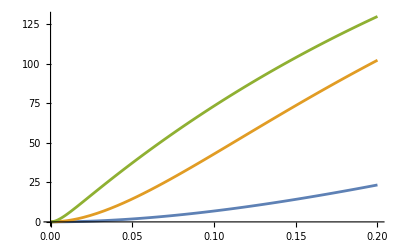

```mathematica
Plot[{c[t]/.soln1,c[t]/.soln2,c[t]/.soln3},{t,0,0.2},PlotRange->All]
```

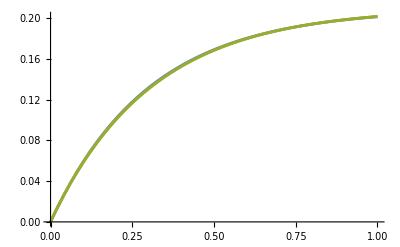

```mathematica
Plot[{p[t]/.soln1,p[t]/.soln2,p[t]/.soln3},{t,0,1},PlotRange->All]
```

Only dissolved oxygen significantly depends on kL. The headspace of the reactor is large compared to the gas flow rate; consequently, it takes a long time for the headspace to change concentration from 0 following sparging of the reactor with N2.

Change the experimental approach and model. Sparge the reactor with N_2. After the DO is low, rapidly exchange the gas headspace with air by using a small computer fan so the headspace O_2 concentration rapidly equilibrates with the atmosphere. In this setup, modeling the oxygen partial pressure can be removed and only a model for DO is needed. Here p[t] is set to 0.21 atm.

```mathematica
odes[input_List]:={
c'[t]==(fL(cF-c[t])+kL a(p[t]h-c[t]))/vL,
c[0]==cF}/.input
```

```mathematica
soln1=NDSolve[odes[{fL->0,cF->0,kL->.13,a->π 0.114^2,h->hO2[298],vL->3/1000,fG->1500.72/1000,pF->0.21,rGas->0.082057338 10^-6,tK->298,vG->4.74/1000,p[t]->0.21}],{c[t]},{t,0,10}]⟦1⟧
```

{c[t]→InterpolatingFunction[…][t]}

```mathematica
soln2=NDSolve[odes[{fL->0,cF->0,kL->1.3,a->π 0.114^2,h->hO2[298],vL->3/1000,fG->1500.72/1000,pF->0.21,rGas->0.082057338 10^-6,tK->298,vG->4.74/1000,p[t]->0.21}],{c[t]},{t,0,10}]⟦1⟧
```

{c[t]→InterpolatingFunction[…][t]}

```mathematica
soln3=NDSolve[odes[{fL->0,cF->0,kL->13,a->π 0.114^2,h->hO2[298],vL->3/1000,fG->1500.72/1000,pF->0.21,rGas->0.082057338 10^-6,tK->298,vG->4.74/1000,p[t]->0.21}],{c[t]},{t,0,10}]⟦1⟧
```

{c[t]→InterpolatingFunction[…][t]}

Equilibrating the headspace with air results in much different DO response depending on kL value.

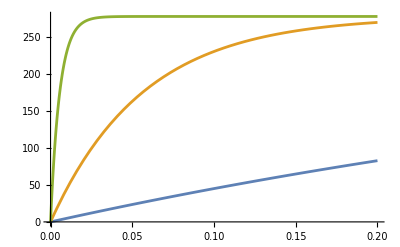

```mathematica
Plot[{c[t]/.soln1,c[t]/.soln2,c[t]/.soln3},{t,0,0.2},PlotRange->All]
```

### Estimate kL based on DO observations Only

Since we quickly equilibrated the headspace with air after driving the system anoxic with N_2, the governing ODE only needs to track dissolved oxygen (DO), as the gas phase remains constant as it is in equilibrium with air.  Here is the governing equation for DO.

```mathematica
odesDO[input_List]:={
c'[t]==(fL(cF-c[t])+kL a(p[t]h-c[t]))/vL,
c[0]==cF}/.input
```

The Henry’s constant as a function of temperature (K) for oxygen (see https://henrys-law.org/henry/casrn/7782-44-7) in μM atm^-1 is:

```mathematica
hO2[tk_]:=0.00131722 ⅇ^(1700(1/tk-1/298.15))10^6
```

Below solves the ODE and plots the solution versus the DO observations.  The only parameters adjusted here are the oxygen piston velocity, kL (m d^-1), which was the objective of the experiment and the oxygen concentration in the atmosphere, p[t] (atm).  Note, it should not have been necessary to change p[t], as it should be 0.21 atm; however, our DO probe may not be perfectly calibrated (or perhaps the headspace still contained some of the N2 gas used for purging) and is reading a bit low; consequently, the O_2 concentration was decreased to 0.177 atm in order to get a good fit.  The value found for the piston velocity is 1.65 m d^-1, which is pretty close to the estimated value of 1.3.

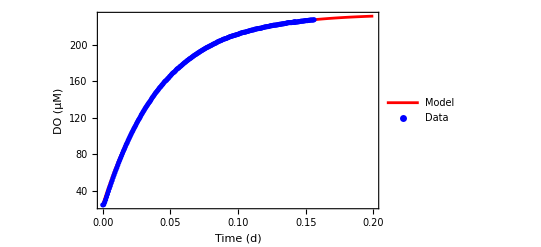

```mathematica
Show[Plot[Evaluate[c[t]/.NDSolve[odesDO[{fL->0,cF->24.7,kL->1.65,a->π 0.114^2,h->hO2[298],vL->3/1000,p[t]->0.177}],{c[t]},{t,0,10}]⟦1⟧],{t,0,0.2},PlotRange->All,PlotStyle->Red,FrameLabel->{"Time (d)","DO (μM)"},Frame->{{True,False},{True,False}},PlotLegends->{"Model"}],ListPlot[o2DataN2,PlotStyle->Blue,PlotLegends->{"Data"}],BaseStyle->{FontSize->15,FontWeight->Bold}]
```

## Governing Equations for Trait-Based Model

### Adaptive Monod Kinetics

The adaptive Monod equation, written as the specific substrate uptake rate, v, not the specific growth rate; that is, μ = ϵv.  Standard parameters are used here. This function chooses along a continuum from gleaners (ϵ → 0) to opportunists (ϵ →0.7). Note, as ϵ exceeds 0.77, uptake rate decreases due to loss of thermodynamic drive (i.e., growth  reaction approaching equilibrium). Also see Vallino & Huber (2018) doi: 10.3389/fenvs.2018.001000

```mathematica
v[s_,ϵ_]:= vM ϵ^2 s/(s+kM ϵ^4)(1-ϵ^2)
```

The adaptive Monod equation gives the following family of curves for different values of ϵ for the standard values of vM (350 d^-1) and kM (5000 μM).

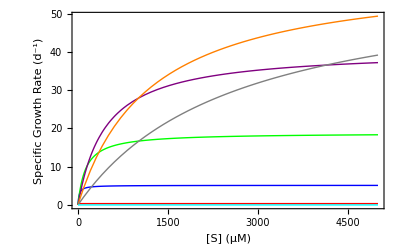

```mathematica
Plot[Evaluate[Table[ Tooltip[ϵ v[s,ϵ],ϵ],{ϵ,0.1,1,0.15}]/.{vM->350,kM->5000}],{s,0,5000},PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick},{Purple,Thick},{Orange,Thick},{Gray,Thick},{Cyan,Thick}},Frame->True,FrameStyle->{{Black,White},{Black,White}},FrameLabel->{"[S] (μM)","Specific Growth Rate (d^-1)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16}]
```

redefine the function with the standard values for the parameters set

```mathematica
(* v[s_,ϵ_]:= 350 ϵ^2 s/(s+5000 ϵ^4)(1-ϵ^2)*)
```

### Saturated Oxygen in saline water

This function, satO2, returns the oxygen concentration (in μM) for a given temperature (K) and salinity (PSU) in equilibrium with air in seawater .  Reference Weiss1970 : (in deep - sea research, 17 : 721 - 735) .  However, the modified version here, hO2, allows for different partial pressures of oxygen, and changes the temperature unit to K .

```mathematica
satO2[tK_,s_]:=Module[{a1= -173.4292,a2= 249.6339,a3= 143.3483,a4 = -21.8492,b1= -0.033096,b2= 0.014259,b3= -0.0017,mlToumole = 44.62,t100},
t100 = tK/100;
mlToumole  Exp[a1 + a2/t100 + a3  Log[t100] +a4  t100 + s (b1 + b2  t100 + b3  t100^2)]
]
```

```mathematica
satO2[293.15,0]
```

283.405

This can be used for different partial pressures of oxygen (i.e., not just atmospheric).  Also, if variables are passed to satO2, then the Exp term in satO2 is simplified, but this then leads to problems because of large and small number multiplication.  By ensuring the arguments are numbers, Exp will not be simplified which keeps this problem form occurring.

```mathematica
hO2[s_?NumberQ,t_?NumberQ]:=satO2[t,s]/0.20946
```

```mathematica
hO2[3,298]0.20946
```

253.757

### Setup governing equations where the number of bacteria is specified and the ϵ trait is randomly selected from a specified distribution.

The function generateODEs generates a set of ODEs based on the length of ranSample, where the latter is a list of ϵ_i values chosen from an appropriate probability distribution (that is, ranSample is given).  The initial conditions for x[i][0] is set to 1/n, where n is the number of ASVs used and x[i] biomass of ASV i and has the units of μM C. This version includes simple quadratic mortality weighted by total biomass for closure.

```mathematica
generateODEs[params_List,ranSample_List]:=Flatten[{Table[{x[i]'[t]==𝒟(0-x[i][t])+ϵ[i] v[s[t],ϵ[i]]x[i][t]-m (x[i][t])^3/Sum[x[i][t],{i,1,Length[ranSample]}] },{i,1,Length[ranSample]}],s'[t]==𝒟(s0-s[t])-Sum[v[s[t],ϵ[i]]x[i][t],{i,1,Length[ranSample]}],
Table[x[i][0]==1/Length[ranSample],{i,1,Length[ranSample]}],
s[0]==0,
o2'[t]==𝒟(o2f-o2[t])+kLO2 a(pO2[t]hO2[sal,tK]-o2[t])/vL-Sum[(1-ϵ[i])v[s[t],ϵ[i]]x[i][t],{i,1,Length[ranSample]}],
pO2'[t]==(fG(pO2f-pO2[t])+kLO2 a rGas tK(o2[t]-pO2[t]hO2[sal,tK]))/vG,
o2[0]==o2f,
pO2[0]==pO2f}/.Table[ϵ[i]->ranSample⟦i⟧,{i,Length[ranSample]}]/.params]
```

This  is  an  older  version  of generateODEs that did not include quadratic mortality. This is not used in the current version and has been renamed to generateODEsOld

```mathematica
generateODEsOld[params_List,ranSample_List]:=Flatten[{Table[{x[i]'[t]==𝒟(0-x[i][t])+ϵ[i] v[s[t],ϵ[i]]x[i][t]},{i,1,Length[ranSample]}],s'[t]==𝒟(s0-s[t])-Sum[v[s[t],ϵ[i]]x[i][t],{i,1,Length[ranSample]}],
Table[x[i][0]==1/Length[ranSample],{i,1,Length[ranSample]}],
s[0]==0,
o2'[t]==𝒟(o2f-o2[t])+kLO2 a(pO2[t]hO2[sal,tK]-o2[t])/vL-Sum[(1-ϵ[i])v[s[t],ϵ[i]]x[i][t],{i,1,Length[ranSample]}],
pO2'[t]==(fG(pO2f-pO2[t])+kLO2 a rGas tK(o2[t]-pO2[t]hO2[sal,tK]))/vG,
o2[0]==o2f,
pO2[0]==pO2f}/.Table[ϵ[i]->ranSample⟦i⟧,{i,Length[ranSample]}]/.params]
```

Example, generate a set of ODEs for 3 ASVs with ϵ selected from a flat distribution where ϵ can vary between 0 and  0.7

```mathematica
generateODEs[{},RandomReal[{0,.7},3]]//TableForm
```

x[1]'[t]==-𝒟 x[1][t]+(0.0328449 vM s[t] x[1][t])/(0.0123038 kM+s[t])-(m (x[1][t])^3)/(x[1][t]+x[2][t]+x[3][t])
x[2]'[t]==-𝒟 x[2][t]+(0.158312 vM s[t] x[2][t])/(0.177677 kM+s[t])-(m (x[2][t])^3)/(x[1][t]+x[2][t]+x[3][t])
x[3]'[t]==-𝒟 x[3][t]+(0.0689391 vM s[t] x[3][t])/(0.0376949 kM+s[t])-(m (x[3][t])^3)/(x[1][t]+x[2][t]+x[3][t])
s'[t]==𝒟 (s0-s[t])-(0.0986186 vM s[t] x[1][t])/(0.0123038 kM+s[t])-(0.24384 vM s[t] x[2][t])/(0.177677 kM+s[t])-(0.156457 vM s[t] x[3][t])/(0.0376949 kM+s[t])
x[1][0]==1/3
x[2][0]==1/3
x[3][0]==1/3
s[0]==0
o2'[t]==𝒟 (o2f-o2[t])+(a kLO2 (-o2[t]+hO2[sal,tK] pO2[t]))/vL-(0.0657737 vM s[t] x[1][t])/(0.0123038 kM+s[t])-(0.0855286 vM s[t] x[2][t])/(0.177677 kM+s[t])-(0.0875178 vM s[t] x[3][t])/(0.0376949 kM+s[t])
pO2'[t]==(fG (pO2f-pO2[t])+a kLO2 rGas tK (o2[t]-hO2[sal,tK] pO2[t]))/vG
o2[0]==o2f
pO2[0]==pO2f

Define a function that numerically solves the generated set of ODEs over time from t0 to tf.  Note, experimental time is based on 00:00 30-Oct-2018.  The simulation “begins” when water was collected and placed into the collection container at about 17:00, or at t0 of 0.71 d.

```mathematica
solveODEs[t0_,tf_,params_List,ranSample_List]:=NDSolve[Evaluate[generateODEs[params,ranSample]],Evaluate[Flatten[{Table[x[i],{i,1,Length[ranSample]}],s,o2,pO2}]],{t,t0,tf}]⟦1⟧
```

#### Define function to capture the shifts in dilution rate to match Exp1

First define a smooth and continuous step function, where the steepness of the function is given by σ.  As σ approaches  ∞, the step function approaches a perfect step, which produces discontinuities at the steps that we wish to avoid for numerical reasons. A little trial and error was used to figure out what a reasonable value of σ should be.

```mathematica
stepFcn[t_,tm_,σ_]:=1/(1+Exp[-σ(t-tm)])
```

Then add these together to get the three dilution rates at the experimental step times of 0.84, 15.5 and 20.77 days.

```mathematica
expDil[t_,σ_]:=stepFcn[t,0.84,σ]/10+9/10 stepFcn[t,15.5,σ]+9stepFcn[t,20.77,σ]
```

Here' s what that function looks like over 25 days.

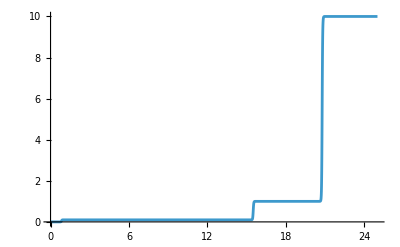

```mathematica
Plot[expDil[t,50],{t,0,25},PlotRange->All]
```

So a value of 50 for σ works well.

Function  for  bar charts

```mathematica
xiBarChart[xiRel_List,labels_List,dBars_List,fig_]:=BarChart[xiRel,ChartLayout->"Stacked",ChartLabels->labels,PlotRange->{{0.5,14.5},{0,100}}, LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},ChartStyle->24,FrameLabel->{"Time (d)","x_i(t) (%)"},Frame->{{True,False},{True,False}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style[fig,Bold,FontFamily->"Arial",FontSize->16],{1,105}],Thick,Text[Style["D = 0.1 d^-1",Bold,14],{(dBars⟦1⟧+dBars⟦2⟧)/2,105}],Line[{{dBars⟦1⟧-0.3,101},{dBars⟦2⟧+0.3,101}}],Text[Style["D = 1.0 d^-1",Bold,14],{(dBars⟦3⟧+dBars⟦4⟧)/2,105}],Text[Style["D = 10. d^-1",Bold,14],{(dBars⟦5⟧+dBars⟦6⟧)/2,105}],Line[{{dBars⟦3⟧-0.3,101},{dBars⟦4⟧+0.3,101}}],Line[{{dBars⟦5⟧-0.3,101},{dBars⟦6⟧+0.3,101}}]},ImagePadding->{{All,All},{All,30}},ImageSize->550]
```

## Uniform Distribution Solution for MS

Look at 500 ASVs with ϵ_i chosen from a  uniform distribution.  Note, each time this notebook is run, a new distribution will be generated.  If you want to use the same distribution, make sure to save it (the one used for the manuscript is given below).

Parameters use for simulations

Notes from Exp 1 state: “Air feed rate to MC1 and MC2 reduced from 20 sccm to 10 sccm (0 °C, 1 atm) (15 : 30 2 - Nov - 2018, t = 3.65 d)”, but just run the gas feed rate constant at 10 sccm for the simulations as the 20 sccm was only run for a short time.
Also, the feed O2 was measured at 20.97 for the first 3.73 days, then either a new air tank was installed or the old one remeasured (probably the former), but that increased the O2 in the feed gas to 21.06, so just use the later for the whole simulation.

```mathematica
params={𝒟->expDil[t,50] (*d^-1*),
s0->600,(*mmol m^-3*)
pO2f->.2106,(*atm*)
sal->3,(*PSU*)
tK->298.15,(*K*)
o2f->hO2[3,298.15].21,(*mmol m^-3*)
kLO2->1.65, (*m d^-1*)
a-> π 0.114^2,(*m^2*)
rGas->0.082057338 10^-6,(*atm m^3 mmol^-1 K^-1*)
vL->3/1000,(*m^3*)
vG->4.74/1000,(*m^3*)
fG->15.72/1000,(*m^3 d^-1*)
vM->350, (* d^-1 *)
kM->5000, (* mmol m^3 *)
m->0.1 (*m^3 mmol^-1 d^-1*)
};
```

```mathematica
uniform1=RandomReal[{0,.7},500];
```

This is the uniform distribution used in the manuscript:

```mathematica
uniform1={0.2065482419257525,0.4172611296271571,0.35183185854095655,0.4366451828429523,0.3560395316384306,0.42449820124996496,0.6809594877225937,0.38842794341524045,0.5847126988356506,0.12897170837409266,0.6597463035814124,0.4014891766117026,0.23870072093247252,0.691996463899059,0.014317448635199903,0.652940269807988,0.2984156979074397,0.4664411076580335,0.3921983780638971,0.6771372386680696,0.17839566115559657,0.35206258907344345,0.5171330447617475,0.41650325004106237,0.29624707718079657,0.45497483718317033,0.392919401893258,0.3732743676998975,0.08501767658279824,0.598904272697989,0.23202487559314888,0.21349869826588597,0.667393800437001,0.3067727707769514,0.6166236165635428,0.6314711452881445,0.3269875087285028,0.05652320530437438,0.2386818464093351,0.23618223486855672,0.42154032217211923,0.5062047536523835,0.23721474795391917,0.13196347011561338,0.22088640475114218,0.699243864658845,0.3116951761916804,0.431017207214462,0.3002163870388015,0.250338211615442,0.29806288030076,0.32310060134129626,0.33340928184110874,0.44892330441803985,0.5570765748832738,0.6653657004231293,0.5762303034727962,0.4839664379219819,0.32493975268700726,0.5213334157672369,0.5152970522232245,0.6598936468281722,0.5386564356001802,0.5232076771678291,0.544446484685907,0.27026510317930574,0.1833846234772416,0.5736104296623166,0.6006094731759439,0.2672580718518641,0.04709393805897244,0.05941964602570604,0.5622078444826373,0.2274815658721403,0.5007093025156355,0.25133611580942705,0.6105546481148267,0.1979532672525618,0.05000807220941472,0.552066823233587,0.2590003935727958,0.237457443753463,0.016898439574316693,0.5721126107501573,0.06465811590082526,0.6363583574943912,0.19032981350339662,0.559154482555692,0.26915324214085745,0.6896679493978137,0.632896679704996,0.5150649385804618,0.43121230981447023,0.4059060326582662,0.6318075104634733,0.2651502889830646,0.41725198184995405,0.6893854894405991,0.041624697186729565,0.019746996267215988,0.14415802609371964,0.10793432544039216,0.362822618693736,0.05922100283814591,0.3421355433833069,0.07993191200692384,0.6226334616255764,0.5207521764740912,0.5929204690868779,0.08851949859515662,0.024743815530322788,0.4215260923680446,0.692383172946867,0.2844521825106663,0.39357078535235956,0.04313401864321609,0.04664460703269424,0.37557069136499965,0.5191583634036083,0.13789813647016524,0.26735140531088375,0.00789442336616597,0.006493044553240734,0.11834930490153739,0.4754075910671882,0.520063609868203,0.6758308528502595,0.11776190213599891,0.40489996300538067,0.5151682312491013,0.5265715848238735,0.42585993926787546,0.6595932369253765,0.5001001019038422,0.10277948543833249,0.19363619115146724,0.6258626927970223,0.10015463157328586,0.44941615196498774,0.6639580030649792,0.24589710316420454,0.296662824322695,0.3222794353065439,0.632920585713636,0.4710608030494874,0.3073407065991345,0.5361889598429055,0.3154393501050501,0.4450246792831589,0.22390945967960085,0.22850025250821604,0.2732681802864583,0.06829244841718873,0.3031393426845157,0.05019573461237692,0.03554777864214709,0.3122836938365021,0.003771339155015485,0.3369145107495395,0.4552134222451223,0.11775377493499473,0.5175914026439326,0.5237186397082338,0.05420197407621552,0.5688008019027067,0.4996714669896485,0.4564187989826092,0.27038034952758283,0.01442339627684297,0.41882803811838465,0.4137107641086115,0.6087810281810224,0.10070729583572058,0.27684253948583837,0.3756644167406118,0.009527840235670992,0.3731076200296297,0.3225264273249502,0.43326904786272125,0.014147089358764187,0.13270432978998092,0.0655469802774602,0.28043454840314586,0.3080004140569841,0.03656213543141551,0.65832884512829,0.26509051825202956,0.3300361486394825,0.4502018712692031,0.04773952093543998,0.2621757604815901,0.6889802476476965,0.629855884807345,0.13984631542686654,0.01757923964267427,0.6104937402581505,0.09934303877249051,0.169071230845382,0.45717267734061284,0.6504508010188645,0.2522272379556365,0.5022273971169731,0.3765684623791232,0.5149103284960848,0.4247873460092446,0.04822777488911689,0.22102623881592098,0.14559108428134138,0.4055362957450488,0.36902889555685725,0.43307663966311116,0.5696344426145243,0.3080624291319367,0.2701104715656921,0.6117185734001893,0.0093902602305459,0.06278858891336392,0.5838417162319471,0.02900780551683335,0.3471502734734766,0.1893819695608724,0.03422406201783146,0.6694259146116552,0.14061068774787966,0.4968517825663361,0.5890820727151236,0.42706637558872274,0.10359572387306759,0.6597840002623023,0.4709404884580477,0.13970276121854897,0.19672091639783873,0.5599146198962612,0.07630275549233345,0.10684108574568352,0.5173521151833715,0.6103963511901886,0.4135177575553539,0.20769641660087623,0.3789065398505702,0.46778882513647213,0.042822853000587524,0.07409679433592253,0.32427759401300893,0.2540107391691374,0.27928681476832284,0.2922690826809595,0.46492661047249584,0.6814345942230915,0.14685698824737725,0.36716847668310026,0.23877521091896214,0.5399763882201027,0.4050280510382773,0.30254017129046673,0.14449246022735462,0.63453056953147,0.17384426833101085,0.4287762953332446,0.3755860451070956,0.28291452467275524,0.5899259142489273,0.24798525127403592,0.34024573256340473,0.11382921457231265,0.1499386193208816,0.4485868723048414,0.4555787169377248,0.13305545599992508,0.3296476973223019,0.16217458133313722,0.3649241587876635,0.24665428324586935,0.3251145789644134,0.3811604931780477,0.26777481529216807,0.3859233829913593,0.39843041442399274,0.21367901211309348,0.3368844187090161,0.5356207438138778,0.19991123084250617,0.08527272409912157,0.370173623904956,0.12751757830050825,0.40558520071674353,0.5723067926812806,0.6695618615760031,0.19040052824921672,0.49440562752954387,0.6809292090875803,0.4994083356666488,0.4032815134252552,0.3309663577180897,0.3413731610458124,0.6351540088058383,0.605694035552284,0.11327180124522707,0.5469156660817527,0.027047039765383474,0.2638053244903391,0.22977235607880309,0.5954757029191076,0.5094477977916994,0.4387785400065811,0.2179903592467023,0.0368866574851715,0.5310169159067182,0.6707172118145324,0.21345597592247656,0.41863771171505215,0.3815895732995318,0.4248102247655767,0.19412481043986296,0.0808361503612387,0.5004663989257818,0.49574593818404367,0.3523246024814899,0.5436841577233462,0.16421278925508076,0.537256442191552,0.22213798017575914,0.29791918320031807,0.2598702747058729,0.34861726597628717,0.6214245108224481,0.41264465422080265,0.13274394601523398,0.46639540530449985,0.2011993651726387,0.29339618979577287,0.17565861330516108,0.6488071870992942,0.48255110726410777,0.3578696701881823,0.48357732694294286,0.5097080668089093,0.29783127068269544,0.5421039541466608,0.5067617238851734,0.5781021129517645,0.105674828699027,0.2418580921410678,0.6359859147360984,0.21614322002293906,0.6514983971431387,0.39478548904559463,0.3844683155403963,0.30969947260076713,0.32649147360537367,0.4947863773287675,0.010521962139906194,0.6494553238693299,0.4294003996078899,0.1929944572220853,0.15469519642795904,0.039917320657550825,0.5260988113956633,0.23579130471925858,0.3371519879451188,0.6290213594015168,0.3281784693720078,0.5858753959171139,0.0205872734250806,0.32211316850911165,0.3464977067174497,0.613194480452915,0.2821644470030129,0.06766244571250635,0.5409083213601404,0.3588434777950602,0.08244302955417204,0.3514519716286213,0.0714344987434734,0.4979492668409198,0.11621559630261902,0.21473308996235463,0.6634217560065465,0.6489452642437117,0.019836432709910534,0.136406482283564,0.37530637999389316,0.6774720266396821,0.5255601276399882,0.447229231764219,0.09499037882820016,0.5422013043958789,0.3953419482650642,0.2166322514574046,0.3281954751520617,0.6623971077752824,0.18101907262714523,0.6241552023459085,0.016511817410057916,0.5391156020265957,0.6662903734546595,0.6561237479173125,0.3068165327549526,0.5552057467067735,0.0898565845336392,0.41748334971300083,0.6295216478605794,0.45415946628305504,0.3254019880735495,0.6275351676978755,0.4008693425916874,0.6280778318971867,0.1305289119835934,0.3577954974155293,0.03815430590973501,0.2717405099220672,0.6634969529024755,0.3615148752261521,0.6842371281532844,0.536276579173385,0.6833934401359436,0.6905416089972782,0.06317887158481994,0.6433864303628316,0.2082159859106154,0.6738000597945417,0.6555720881238061,0.5554346153246026,0.6176525267784809,0.29729638414525184,0.37108743414729295,0.40091978301839504,0.0857563355669333,0.39704447609159343,0.16543233487499953,0.09218986791140704,0.5698681076233858,0.6956767933281949,0.41950240939788275,0.2952400204149369,0.08067700407842804,0.25445234120507754,0.36144733726060085,0.3957455661682834,0.21194023467288614,0.5895714586824707,0.105130076108367,0.4130576892931277,0.15773724076328866,0.0348287500414356,0.13923808962973494,0.5763757494959347,0.3081722320227287,0.10879844961608343,0.063858091223713,0.22018399730578853,0.3330353253304428,0.3453126101695516,0.1919241414515721,0.2412064425045216,0.5305119840694461,0.5279098494207628,0.09222150904942761,0.6242624195065067,0.5902858683907959,0.11540739636530517,0.5043633698671388,0.23482345851686148,0.2223792664108203,0.3334528599286597,0.061433857369995404,0.0747635812348807,0.4563892275506414,0.41160558793918733,0.542439113807941,0.4796261046982988,0.4077866867246682,0.2591494587638222,0.10554280829901075,0.33913813127207737,0.1270218904668956,0.1916306449708426,0.671447992469268,0.37673456646458847,0.15856388976844382,0.5261913306831196,0.528606821109352,0.582104699603283,0.13973327283704529,0.5873707991867072,0.3189383131140051,0.16079910882618154,0.099264140210233,0.3617999954507791,0.14617602634649052,0.01762801396450997,0.6849049180681488,0.6698191461374112,0.6668137282252296,0.44924603983737343,0.006476528919752256,0.17729932817205374,0.49145878512771213,0.5208475936058174,0.334942734026195};
```

Plot the realized probability density function based on uniform1 sample as well as the theoretical one.

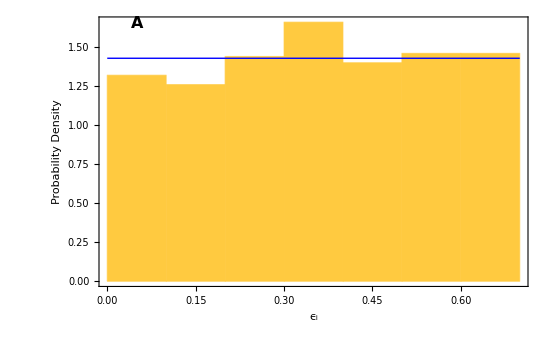

```mathematica
uniformDistributionPlot=Show[{Histogram[uniform1,Automatic,"ProbabilityDensity", Frame->{{True,False},{True,False}},FrameLabel->{"ϵ_i","Probability Density"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18,FontColor->Black},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["A",Bold,FontFamily->"Arial",FontSize->16],{0.05,1.65}]},ImageSize->550],Plot[PDF[UniformDistribution[{0,.7}],x],{x,0,.7},PlotStyle->{Blue,Thick}]}]
```

```mathematica
Export["uniformDistributionPlot.svg",uniformDistributionPlot]
```

uniformDistributionPlot.svg

Solve the 500 ASV ode equations for the uniform distribution

```mathematica
soln500=solveODEs[0.71,24,params,uniform1];
```

500 ASVs for the uniform distribution case  in absolute concentrations (μM C).

```mathematica
Rasterize[xiUniformPlot=ListLinePlot[Evaluate[Table[{t,x[i][t]},{i,1,500},{t,0.71,24,0.1}]/.soln500],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","x_i(t) concentration (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18,FontColor->Black},PlotStyle->Thick,FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["A",Bold,FontFamily->"Arial",FontSize->16],{2,3.5}]},ImageSize->550]]
```

-Graphics-

Save  this  plot for the manuscript

```mathematica
Export["xiUniformPlot.svg",xiUniformPlot]
```

xiUniformPlot.svg

The Manipulate function below allows you to slide the slider below to look at profile for individual ASVs (μM C). However, this can cause issues with the front end, so it’s not evaluated below

```mathematica
Manipulate[Plot[Evaluate[x[i][t]/.soln500],{t,0.71,24},PlotLabel->"ASV: "<>ToString[i]],{i,1,500,1}]
```

Plot the sum of all ASVs (μM C).

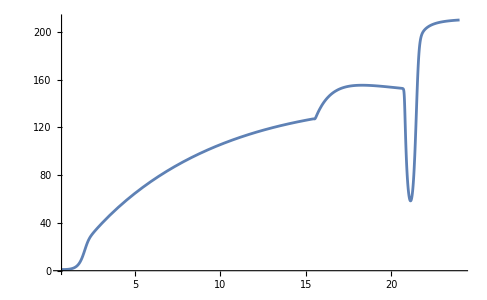

```mathematica
Plot[Evaluate[Sum[x[i][t],{i,1,500}]/.soln500],{t,0.71,24},PlotRange->All]
```

Plot the substrate concentration (μM C).

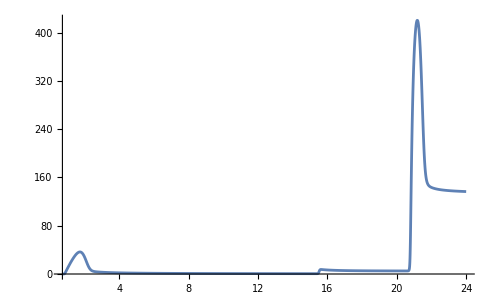

```mathematica
Plot[Evaluate[s[t]/.soln500],{t,0.71,24},PlotRange->All]
```

Look at diversity using relative abundance, and sample at the same times points as the MC’s were. Note, because of the high diversity, the min ASV relative abundance must be set rather low, as no ASV reaches high rel abundance. Here, using 1% (that is, include any ASV that at any times exceeds 1% in abundance)

```mathematica
times={0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5}; 
uniformASVs=Prepend[Evaluate[Table[Table[x[i][t],{i,1,500}]/.soln500/.t->times⟦j⟧,{j,1,Length[times]}]],Evaluate[Table["ASV_"<>ToString[i],{i,500}]]]ᵀ;
uniformASVsRel=Prepend[Table[100uniformASVs⟦1;;,i⟧/Total[uniformASVs⟦1;;,i⟧],{i,2,Dimensions[uniformASVs]⟦2⟧}],uniformASVs⟦1;;,1⟧]ᵀ;
```

With  a  1 %  cutoff, there are not ASVs that make it to the end of the experiment

```mathematica
Rasterize[asvUniformRelGT1=Select[uniformASVsRel,(Max[#⟦2;;⟧]>1)&];ListLinePlot[Table[{times,asvUniformRelGT1⟦i,2;;⟧}ᵀ,{i,1,Length[asvUniformRelGT1]}],PlotRange->All]]
```

-Graphics-

Look at including all ASVs

```mathematica
Rasterize[asvUniformRelGT0=Select[uniformASVsRel,(Max[#⟦2;;⟧]>0)&];
ListLinePlot[Table[{times,asvUniformRelGT0⟦i,2;;⟧}ᵀ,{i,1,Length[asvUniformRelGT0]}],PlotRange->All]]
```

-Graphics-

Plot absolute ASV concentrations and relative abundance at the experimental sample times as a bar plot at the 0.1% relative abundance or greater.

```mathematica
asvMinAbunRel=0.1;
asvUniformMin=Chop[N[uniformASVsRel],asvMinAbunRel]; (* this sets any ASV that is < asvMinAbunRel to 0 *)
```

```mathematica
Rasterize[GraphicsRow[{Plot[Evaluate[Table[x[i][t],{i,1,500}]/.soln500],{t,0.71,24},PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","x_i(t) concentration (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},PlotStyle->Thick,Epilog->{Text[Style["A",Bold,FontFamily->"Arial",FontSize->16],{2,3.6}]}],
BarChart[asvUniformMin⟦1;;,2;;⟧ᵀ,ChartLayout->"Stacked",ChartLabels->{{0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5},Table["",{14}]},PlotRange->{{0.5,14.5},{0,100}}, LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},FrameLabel->{"Time (d)","x_i(t) (%)"},Frame->{{True,False},{True,False}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},ChartStyle->24,Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16],{2,97}]}]},ImageSize->1024]]
```

-Graphics-

Bar Plot alone

```mathematica
Rasterize[xiBarUniformPlot=xiBarChart[asvUniformMin⟦1;;,2;;⟧ᵀ,{{0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5},Table["",{14}]},{1,5,6,9,10,14},"A"]]
```

-Graphics-

Save  this plot for the manuscript

```mathematica
Export["xiBarUniformPlot.svg",xiBarUniformPlot]
```

xiBarUniformPlot.svg

Export the ASVs table for the time points that correspond to all sample times

```mathematica
Export["uniformASVs.csv",Prepend[uniformASVs,Flatten[{"ASVs",times}]]]
```

uniformASVs.csv

Export the relative abundances with no cutoff

```mathematica
Export["uniformASVsRelative.csv",Prepend[uniformASVsRel,Flatten[{"ASVs",times}]]]
```

uniformASVsRelative.csv

### Uniform Distribution #2

Select another uniform distriubtion for statistical comparison like the experiment

```mathematica
uniform2=RandomReal[{0,.7},500];
```

```mathematica
uniform2={0.5165735824339561,0.1980857886199866,0.4143254015176081,0.4783368871369138,0.1034833654725913,0.526057482775403,0.6003021079433981,0.6435859570869096,0.2602062799741649,0.6633169315693819,0.5081218474069846,0.20415279866263358,0.5278481183286174,0.11830099776804737,0.5233252611126566,0.6625346195826904,0.6987746808677391,0.4129498202618569,0.4359497182563976,0.42257969641459536,0.28925741679143335,0.1244195313625831,0.02570299998278025,0.6881473184918472,0.6796156477464579,0.02516230538110109,0.4818043378126342,0.409648335626003,0.4825195483064324,0.1961683709727149,0.6688246267190816,0.5746151136287843,0.32561340661435234,0.04985249566718797,0.37626409069621713,0.4181657721138998,0.5468226976656663,0.18276444147990423,0.037845280861015795,0.2627361368894816,0.5418846992362616,0.47064719582168246,0.20647480301157084,0.07940096049795486,0.12597594941374712,0.15136172142951465,0.2790833221111445,0.43677983647314234,0.5348098193472786,0.05772422601877192,0.3869401255836358,0.1627598744695491,0.2753308782175764,0.34018732253669515,0.32082057521118346,0.21571087139181622,0.5091090447778415,0.15799593455834693,0.2801675363298336,0.041561419006605815,0.6531945737125919,0.5839968902315966,0.2227040995610915,0.4751439062379095,0.14687157027886089,0.5851568500847735,0.07917146589263901,0.32167245788535004,0.37640141733055765,0.6472017782757409,0.435300361654948,0.35873148823236645,0.6786271103209036,0.6248676918705169,0.27874126260037646,0.21725974667701353,0.009288770433434235,0.3675586693228632,0.20399747000519242,0.3061369447963267,0.3716063372293874,0.18824644787574618,0.6029677508646796,0.09996195575556754,0.0010969928648916216,0.3457502107579564,0.5546526823063977,0.33334806146016005,0.6372037958809165,0.5414804746435036,0.4700095545044902,0.6389303710876073,0.4698993119385908,0.6719053769859114,0.45393827744106185,0.03312602461994374,0.06379337932149398,0.696419299914357,0.6660908156791834,0.42740586141557846,0.2682301563106432,0.10050975665381268,0.2258995810191421,0.2222474551426712,0.6776526738009501,0.33146883912557534,0.5766151782308202,0.5761868881689047,0.42066715674064303,0.3189877221478097,0.643419724169805,0.396411217481778,0.1614963351656744,0.1456500851345368,0.2675311506302238,0.11497636154691326,0.3884832391969504,0.1400015022195894,0.4337937485898615,0.11699538389462905,0.28985575834732413,0.4141110178302123,0.1187557383354082,0.31112563138752236,0.1654153126443625,0.13313758486057248,0.05807637517945652,0.04756103904733833,0.11783269050096823,0.5444679843484153,0.48763480015343896,0.5889152395402824,0.43577196812212926,0.2307824727283171,0.2714166757740517,0.23660254203688724,0.1309227173141928,0.17909580375171175,0.5166233486933944,0.1018686812157682,0.6692784029229466,0.31085154543164073,0.03788924824078321,0.2904486623044715,0.5064032193802637,0.1610055683912066,0.6373753797172985,0.3093614022482536,0.2572112778534722,0.5303486098396808,0.02971575622964928,0.6498413705112394,0.44849904391707796,0.17422446823289783,0.46072225340883977,0.5505875244476541,0.32468275915553546,0.3188275266443692,0.15011989962064098,0.006606218049896362,0.40070740735791954,0.15211744488306322,0.179059904786127,0.6967508357000094,0.6506125135530891,0.16194254638695982,0.1965236139836951,0.5416323775449332,0.4448315904702016,0.19486284788003072,0.6108263962751426,0.053293937418018356,0.3381688958252065,0.1360251395416534,0.48036507091131986,0.24931595289474118,0.0028739417088263775,0.2053810168947613,0.6003672062570959,0.05162896841627196,0.1559373778014812,0.3050100081317444,0.5325944961132172,0.314357338170673,0.5405917522706358,0.45195874514635337,0.1665373077096446,0.39566964318415154,0.4757429787193921,0.3786554212086959,0.0576892018745051,0.0764841725570996,0.44758940579572104,0.2766194413865999,0.5124319561321193,0.6172561432364949,0.13754244439631524,0.43078860808025143,0.005732961276525339,0.5274973870295936,0.37559172935996865,0.3890439232286418,0.1741783946595058,0.6409909731811023,0.4784312834060902,0.4066162539357674,0.4605509272724748,0.05719671367516632,0.28328274929436625,0.2955102427858013,0.10478726432102892,0.22198352610819427,0.6523463488354915,0.47789052703298385,0.671961368865394,0.0970575983550368,0.45928717085240867,0.410260276322288,0.12597891836974973,0.3689666621956309,0.3989021259183865,0.021011197643441837,0.023657582263952648,0.02854901122353093,0.4773651884272978,0.272324033230709,0.14263801546271349,0.07055984746579058,0.5932584391675224,0.09077035524602162,0.19410301961523857,0.15930211014385842,0.3187249221974382,0.06246434403936485,0.5780682815599654,0.4908828490313615,0.6635552946114238,0.36052254060296507,0.6417898716062753,0.18161766592702455,0.2821822408997936,0.29837492835213975,0.09230212163403384,0.39153912594036466,0.5425639628824961,0.4630512535534921,0.0791671756446094,0.33224732112416655,0.41740157027001223,0.16591127129205574,0.5577084518697384,0.5508168273503622,0.26111542833480295,0.6805643909279124,0.2014791608842854,0.32104827936289637,0.0020771197631004323,0.34413690931674235,0.41979587529627005,0.5553780309210914,0.573057585045128,0.20713530234506705,0.5621441159264471,0.017345470907808358,0.4906176379616878,0.6354480136866993,0.2249936162653693,0.5986385500121509,0.5884170625749978,0.1945466188845767,0.1548635834939499,0.22406541578998795,0.28568689142737014,0.3732500665888119,0.6086656269688304,0.6416022475961962,0.6598468905438626,0.35469520754174,0.32830842252879733,0.5444918572293118,0.38106681085792915,0.5011273652117225,0.617418606271434,0.6333370367783608,0.34372516318416113,0.28378802397818936,0.5391350018569758,0.23673183280023657,0.4762879059132006,0.034134132184376775,0.3457998797755728,0.24679008374085576,0.6761103480527411,0.5704331935346867,0.5397040237847961,0.5814481953724806,0.17879920378986647,0.1321899639651466,0.4367260125441208,0.24706983501616764,0.062110011472131244,0.5247834938817504,0.5962403057455443,0.17221168147670285,0.6427583374071104,0.011415660169478259,0.2339174070437512,0.5499916095403083,0.4268317945198643,0.5135944209285206,0.45731917320096427,0.04887028142423688,0.6869240994323815,0.0655124711326287,0.4971247167683621,0.3893159432548985,0.0318384385736491,0.25059989776193614,0.1478380001259444,0.19020671473598816,0.3119373699524286,0.12241952701633962,0.052611662275015236,0.4671868430427413,0.515213090299927,0.059969824173541686,0.3852155147367575,0.5190904691500349,0.4458549229266444,0.44083405849753476,0.5660762036360527,0.17250486652701102,0.22031327564357195,0.3007469876293296,0.020434306191566498,0.28410631304395517,0.3038151108672782,0.17521234546137665,0.1160909946220785,0.012245444653854465,0.1542462850361659,0.20453505784800496,0.03915861102234652,0.2723637222016322,0.48127108021753595,0.023941985622894957,0.47734391822294064,0.5004223667096519,0.4543445754825697,0.6012129742810082,0.6271640879840856,0.3325787624664218,0.3824425153019402,0.4581603966474028,0.6392806829430093,0.04592183543416173,0.1818630492771396,0.3305544904355395,0.19282004652951523,0.04631252947706732,0.4141114296650168,0.08657163979388605,0.4761019500425818,0.0039023679913331444,0.43686536623730565,0.34946098995677044,0.08319342729729451,0.44750222251663163,0.17153633247409295,0.4742003546314202,0.42269848410547506,0.4007506426519911,0.45172090027176304,0.6779312418654397,0.6038999258553812,0.10617212932112563,0.12188009384653142,0.6570598186911727,0.17334867911086627,0.25319267625806907,0.6614204831777646,0.3571003533861503,0.3242339618524481,0.2602290303777195,0.3097652308184642,0.13112803822516894,0.3872956215735568,0.317398345044289,0.008366104879790282,0.014332623247805154,0.3651007593452573,0.07137193323925106,0.44160083090865987,0.39703322471332303,0.5824913231991671,0.012819903157630264,0.12182065402854936,0.2924247417506166,0.4961281007068987,0.4458455048184664,0.48363908021565627,0.5120347597946684,0.5751814444524226,0.561169793128174,0.3679347272706701,0.2171347873673669,0.32252856768694493,0.0579280900897543,0.5348232235856691,0.12239207111416883,0.17459326949606735,0.11043873482333566,0.20921837242680197,0.11221016184649557,0.14507614070745278,0.12566205978920697,0.05027700373352295,0.5695238262083511,0.6893510161689107,0.6435735931507789,0.21440275247751794,0.39743791734226286,0.6941516686846618,0.564821138207465,0.010374553534024167,0.038215136937455374,0.2365486961419384,0.5930592117504718,0.23729944952851645,0.2773915011736654,0.024829199904495614,0.080267340053362,0.4100418465746878,0.23222071108672082,0.43607658677258554,0.5139983656965705,0.3739591099053825,0.6952762892428317,0.5316543494924388,0.5455374720948576,0.42040469275229153,0.32503328488524086,0.43309543943253104,0.08879787074400458,0.4826758359272785,0.5994206615488782,0.4639811031266068,0.29850423574882146,0.17906917112887233,0.1953001423725409,0.03025929739673283,0.5235075500488184,0.568476975248497,0.20402773497392357,0.525536087702092,0.5456446214589117,0.07861011693670483,0.6140315978943838,0.4916413329115321,0.5714279173635017,0.5054078566206923,0.5817019603536946,0.5218980635560444,0.2985894204964593,0.4991199280210179,0.1438885971787165,0.6002041677762422,0.5524606061649737,0.0003203607085954241,0.5616684770155649,0.3485915402838018,0.4878243092682686,0.48232631236460133,0.5246158286927993,0.2690026031113396,0.6549148911997813,0.15589519336581348,0.5860115236609147,0.5724221689221705,0.00267509632032803,0.5709780804571862,0.20732464988693178,0.49634343601838693,0.6831567741198707,0.2359589168927726,0.09228088070002927,0.48246575223662025,0.30866612269726357,0.39427830027807875,0.429371617526757,0.03357609230469949,0.4123464742555827,0.608360013504452,0.2565265598855999,0.032315271202563944,0.4636726288485069,0.6446299162462004,0.2872935822591598,0.38686348877416554,0.4925557734597801};
```

```mathematica
soln500b=solveODEs[0.71,24,params,uniform2];
```

```mathematica
Rasterize[xiUniformPlot=ListLinePlot[Evaluate[Table[{t,x[i][t]},{i,1,500},{t,0.71,24,0.1}]/.soln500b],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","x_i(t) concentration (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18,FontColor->Black},PlotStyle->Thick,FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["A",Bold,FontFamily->"Arial",FontSize->16],{2,3.5}]},ImageSize->550]]
```

-Graphics-

```mathematica
times={0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5}; 
uniformASVsB=Prepend[Evaluate[Table[Table[x[i][t],{i,1,500}]/.soln500b/.t->times⟦j⟧,{j,1,Length[times]}]],Evaluate[Table["ASV_"<>ToString[i],{i,500}]]]ᵀ;
uniformASVsRelB=Prepend[Table[100uniformASVsB⟦1;;,i⟧/Total[uniformASVsB⟦1;;,i⟧],{i,2,Dimensions[uniformASVsB]⟦2⟧}],uniformASVsB⟦1;;,1⟧]ᵀ;
```

```mathematica
asvMinAbunRel=0.1;
asvUniformMinB=Chop[N[uniformASVsRelB],asvMinAbunRel]; (* this sets any ASV that is < asvMinAbunRel to 0 *)
```

```mathematica
Rasterize[xiBarUniformPlotB=xiBarChart[asvUniformMinB⟦1;;,2;;⟧ᵀ,{{0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5},Table["",{14}]},{1,5,6,9,10,14},"A"]]
```

-Graphics-

```mathematica
Export["xiBarUniformPlotB.svg",xiBarUniformPlotB]
```

xiBarUniformPlotB.svg

```mathematica
Export["uniformASVsRelativeB.csv",Prepend[uniformASVsRelB,Flatten[{"ASVs",times}]]]
```

uniformASVsRelativeB.csv

```mathematica
Export["uniformASVsB.csv",Prepend[uniformASVsB,Flatten[{"ASVs",times}]]]
```

uniformASVsB.csv

## Beta distribution function Solution for MS

This is basically the same as above, except ϵ is drawn from a beta probability distribution that is skewed towards oligotrophic growth characteristics.

#### Run with α = 1.1, β = 13.3

```mathematica
params={𝒟->expDil[t,50] (*d^-1*),
s0->600,(*mmol m^-3*)
pO2f->.2106,(*atm*)
sal->3,(*PSU*)
tK->298.15,(*K*)
o2f->hO2[3,298.15].21,(*mmol m^-3*)
kLO2->1.65, (*m d^-1*)
a-> π 0.114^2,(*m^2*)
rGas->0.082057338 10^-6,(*atm m^3 mmol^-1 K^-1*)
vL->3/1000,(*m^3*)
vG->4.74/1000,(*m^3*)
fG->15.72/1000,(*m^3 d^-1*)
vM->350, (* d^-1 *)
kM->5000, (* mmol m^3 *)
m->0.1, (*m^3 mmol^-1 d^-1*)
α->1.1,
β->13.3};
```

Look at 500 samples taken from the beta distribution for α = 1.1 and β = 13.3

```mathematica
betaSample=RandomVariate[BetaDistribution[α,β]/.params,500];
```

This is the beta distribution used in the manuscript

```mathematica
betaSample={0.04871417003885394,0.03017318186219966,0.012564993680192262,0.13259384803132962,0.021620267469453208,0.2344049750022628,0.15149911540580235,0.004684454408583026,0.004601369086191348,0.042992808450216524,0.025453219010936827,0.09417271597016663,0.045696091326077035,0.13284625263752917,0.0266933889076973,0.2629338141682852,0.059354581681200495,0.07931635152117568,0.2205508867126184,0.02118909371323286,0.08205366876494401,0.010931389024451262,0.1496050188706156,0.05525010558659861,0.15288468109095826,0.015915678507397803,0.031122272663232253,0.0803226560606708,0.04314709139378374,0.14315676215797007,0.058359206495349786,0.18170250048485312,0.03360900445255381,0.02942456554931353,0.2087416396838662,0.0054045809746471685,0.0013462079542849493,0.07212716572067226,0.10450967555532742,0.08744099507163389,0.09493157153736054,0.0784467555946978,0.05166651168990486,0.001334149348788744,0.07578982056455534,0.037153957616935386,0.005309644300830824,0.15411445948443941,0.009751849308989518,0.07225647802771631,0.06936608679819813,0.06120727001345328,0.12843678844929338,0.042131323662609736,0.01672018869895678,0.015215508943382137,0.11225009904324758,0.04919497886917243,0.0188384047140116,0.037266167674637106,0.11093762041353886,0.12789992411848625,0.12052621965819525,0.010627490500548538,0.01826746581890762,0.023365705979300037,0.02368827336416486,0.0739020305574193,0.011295655622854098,0.05408094424198332,0.1490046520058161,0.12578634491357937,0.004869659200823763,0.26630301156497094,0.003849534540199007,0.06905215114004311,0.06859481953405061,0.028748724748098115,0.14847369252819873,0.2174523572636497,0.193708893081989,0.07714866769087032,0.022871419185523347,0.06341184944387644,0.12244641637062309,0.11624046267496087,0.07164536542764394,0.08039840001044087,0.052431646380330536,0.10668348177075203,0.09154832908079456,0.03257046394954066,0.09198072965736782,0.12734788662242694,0.1615990690664287,0.0007023097483443249,0.04599757673754196,0.1420387979824347,0.02609236076796676,0.05483319833189066,0.0034541546335561378,0.059798268076024244,0.022552148777120484,0.023829340082174116,0.03753009055321549,0.15590155990015542,0.13292412426629985,0.0031347163603508955,0.005809975013229053,0.05347731920469983,0.1195926517599274,0.024169207539693684,0.033868128972670254,0.0047255961787532365,0.009001096613049143,0.05456996503276114,0.015376698457814768,0.03673534349017801,0.0442168643374372,0.004980503399767064,0.06866586347795299,0.039909944942066865,0.024100042679365354,0.06122708284578606,0.12067197707201006,0.22428778681067332,0.10321455171062971,0.061810528166035536,0.03429125097271478,0.009354432062220638,0.13554475676696812,0.05585587463340101,0.0011726470568291143,0.01148917385931319,0.0035962648649721933,0.03181949730803888,0.2267838072655365,0.16117554712647378,0.02698462446839613,0.010845142280690185,0.023816314095584358,0.13052320860442276,0.024311528150703785,0.027374071069603177,0.002366588015184559,0.024849074414056854,0.2439961188452165,0.0235668780209888,0.021101438545775366,0.003727398656108021,0.22215983371715115,0.06126381635770991,0.03857094915832731,0.010191563790865634,0.09609645624578363,0.02155436426391609,0.0497287884915788,0.027378315530424253,0.10126542602303192,0.11074720582468918,0.059013521119175315,0.08009191489674815,0.026025990574873595,0.0516453688165229,0.436635733572928,0.09505766406257224,0.18151396744044626,0.004026497589513533,0.08694990562535915,0.010689776034261059,0.06093180898944036,0.14815681455394025,0.017389728855135546,0.15376068053083183,0.10547790711750345,0.053319059254476144,0.007828492425429658,0.11547561707596206,0.001962946563101294,0.020742429167826728,0.09263697203414759,0.11065848773597486,0.06350342699675426,0.22296694310636778,0.08771449197198464,0.04811220738693807,0.03711701562767455,0.037113529737442814,0.1275420670922201,0.10890010804702391,0.0010086477888882534,0.12210310077445455,0.032606956528330545,0.03526221608701037,0.17583830800943565,0.06714135752884476,0.09828443656338597,0.0009216775278314409,0.1705419780457287,0.03811325289180692,0.047644995061664995,0.021183078103196543,0.13362095999997362,0.01524195729847747,0.012765560839104026,0.012902106693768548,0.09892142768556995,0.03809981023599537,0.09142479321216293,0.02117021052803575,0.01790428904971133,0.023014618759056738,0.041208699630478025,0.1604234626667358,0.13624906440479095,0.2172044212009787,0.01472299488027583,0.10320904273889435,0.03538900540536,0.15383534367786517,0.0831765127288058,0.2891594570145767,0.012784100076480495,0.058137248081689574,0.07989725697937083,0.03750493565627171,0.030127139394336866,0.0692569612013841,0.1057124791160422,0.07636299363027825,0.02805523454207417,0.09803811080087738,0.0040968904614844814,0.18555557437046988,0.13923635889454775,0.054409267476525254,0.07170089091396022,0.17785360980939177,0.08703292497589263,0.11066124950446958,0.01849525339465957,0.01125351097552394,0.02617265456166756,0.028703125286146262,0.02435163110964077,0.14764131913850376,0.04282363862056955,0.016388741616495523,0.0024044815732956557,0.06621756332129385,0.08482442792532743,0.0972863022943594,0.06252463091101566,0.006323773999152156,0.07362815024186246,0.0611440977466474,0.07972642169305205,0.1447556892689672,0.09928994351387667,0.020794784747151036,0.050520000331074226,0.12141743932292878,0.036350985169579256,0.01753499671893606,0.09981444140966093,0.3040912124150068,0.21577960371639454,0.12282298401480057,0.005609713311279573,0.014979100908650154,0.03170198434798988,0.008771309668806833,0.12799598858285297,0.18253831146701313,0.22604220035805841,0.022101791111936452,0.17276189858838992,0.08861263428291366,0.04812472719891856,0.046674493469162186,0.021464146507729518,0.16044991188722343,0.0466983600698937,0.06957677647088273,0.09043801855017315,0.1644442606878382,0.12545534607706213,0.08260742429007133,0.08309558671739452,0.014564491167656008,0.07667963494845564,0.051622435206747475,0.12374328132302406,0.002498968309387258,0.013030313862055545,0.006428129906045408,0.05001626077167433,0.026443982143654638,0.0539879735120826,0.1312999823623269,0.11512505634597918,0.21686950178922165,0.13585031425223854,0.07210004355656577,0.04793868805193183,0.09283559178732992,0.08969893726785652,0.1127165179660344,0.10775185052769168,0.082934653731241,0.06823372191103245,0.06587945352658324,0.2328410568252529,0.29667855682759264,0.2417366751952173,0.02268594766727997,0.10536656975095389,0.041595829142700776,0.022853557801980416,0.14210978074465158,0.0832995335530726,0.042037241378529315,0.1356399267952631,0.1019334755670714,0.017516502335782242,0.09479937599913722,0.10588947742985351,0.027886623944396186,0.04829511408747073,0.05377671868006312,0.027548383900668754,0.10032500675730449,0.0025943474034798727,0.0002914995586228621,0.11763744700827708,0.10308827759380966,0.07394200450453615,0.10622159011543529,0.014848515802661616,0.25550171739791566,0.2053131811836873,0.0017261960196748958,0.06294153015556311,0.01920130174043932,0.03554558881839803,0.0791365044139423,0.026971779170970305,0.07574165069700076,0.1421689759972292,0.09329687854788936,0.05024255981023416,0.0490125971519095,0.022976297480557004,0.029544565269354898,0.15065479884821742,0.008209166237822623,0.17455831112154385,0.013752289171807503,0.07422293537549755,0.1639564288054622,0.14087312121450782,0.014014135664685779,0.0027830560397054402,0.16666839002916034,0.026505413568927255,0.11446821433343855,0.11050762219668844,0.00541900015390286,0.037520865133616896,0.030772458132362467,0.05280786810800987,0.03407556710718542,0.03084800257306437,0.10102930634113923,0.13044375778720677,0.030600156418795557,0.010512867983209667,0.1274287373380895,0.17745371321519915,0.11057254754925154,0.007516639911862173,0.026979097585571113,0.002611592186387166,0.0337798156974438,0.05597223108797968,0.04911962522972667,0.13053360462565602,0.12067387539058357,0.11878864049784978,0.1250216585092904,0.12074100130465794,0.20558704294754135,0.14246463035757395,0.07402279649358105,0.07786475965990819,0.0340581506060693,0.08041523444578938,0.01558213710139311,0.16397534159102004,0.11779291952672884,0.017105792256956742,0.08357290011776101,0.23607846408267072,0.040883668439963376,0.03321036888035268,0.04703692179272006,0.1166662308048623,0.0038126213775626595,0.07725972617027421,0.01032278551667974,0.13436662312586525,0.36570938724633445,0.10770468048277729,0.01296953141933141,0.04731132700667836,0.044446624328923344,0.00618235122746949,0.05300837236083615,0.10050303763689357,0.190210728684964,0.0513335253832927,0.11537750376189984,0.4878235997476536,0.009631465023873832,0.16066235202414658,0.17448920272235646,0.0816645835667271,0.21018687411435585,0.06529908683101382,0.14954184309941784,0.03624690107933765,0.02128298021358151,0.025108762686227807,0.10885757617356026,0.015409928243411416,0.05263634391372248,0.013831751270294623,0.1400540494420741,0.00406843759633261,0.07963999651514335,0.07330640592822639,0.07304679090028407,0.005040331979276583,0.05734420056467882,0.021502024380563593,0.03827259182580616,0.10814138756654423,0.12808460159445015,0.06217340387635631,0.031154479356549615,0.12116323038579138,0.010500654548535904,0.06516840129529362,0.03301747044044952,0.07547029436558676,0.04258003424194382,0.04384589188197849,0.03184852282369526,0.0780225475565889,0.01872239907846052,0.07086199931284655,0.010902596630949998,0.13966318078624584,0.040832296776574635,0.03782425997615499,0.06320106847160721,0.052262142440238066,0.04638169643741573,0.04276469913748643,0.12672730542857397,0.0456168335292967,0.05412109296934094,0.11581652833622333,0.078930530472329,0.04601024282871352,0.1506702363443959,0.07005305360127806,0.047111011427714684,0.017198257945144423,0.111219962811526,0.205405329278806,0.09596661055086143,0.0031196112401487386,0.049203736550980134,0.188870226685046,0.09812922801643555,0.04157488368849383,0.1878757151311634,0.06781604975098905,0.13737459056442122,0.0017052641579928189,0.01147809467931195,0.10381208418397085,0.09294383557583803,0.025770371736442615,0.0766033200309779,0.04359861555511431,0.0015258878654216925,0.130528588016478,0.15164736597095563};
```

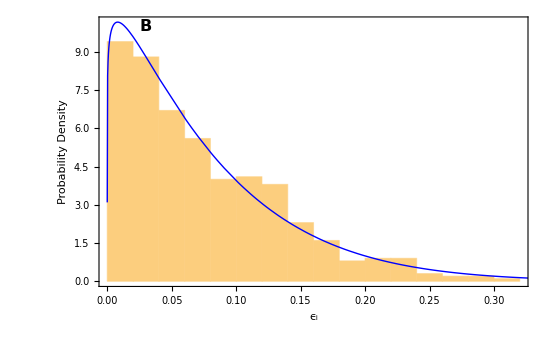

```mathematica
betaDistributionPlot=Show[Histogram[betaSample,Automatic,"ProbabilityDensity", Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",""},{"ϵ_i",""}},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16],{0.03,10}]},ImageSize->550],Plot[PDF[BetaDistribution[α,β]/.params,x],{x,0,1},PlotStyle->{Thick,Blue},PlotRange->{{0,0.7},All}]]
```

```mathematica
Export["betaDistributionPlot.svg",betaDistributionPlot]
```

betaDistributionPlot.svg

Solve ODEs for 500 ASVs again, but using the sampled beta distribution.

```mathematica
soln500beta=solveODEs[0.71,24,params,betaSample];
```

Plot  the  absolute  concentrations  over  time

```mathematica
Rasterize[xiBetaPlot=ListLinePlot[Evaluate[Table[{t,x[i][t]},{i,1,500},{t,0.71,24,0.1}]/.soln500beta],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","x_i(t) concentration (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18,FontColor->Black},PlotStyle->Thick,FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16],{2,70}]},ImageSize->550]]
```

-Graphics-

```mathematica
Export["xiBetaPlot.svg",xiBetaPlot]
```

xiBetaPlot.svg

Look at relative abundances

```mathematica
times={0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5}; 
betaASVs=Prepend[Evaluate[Table[Table[x[i][t],{i,1,500}]/.soln500beta/.t->times⟦j⟧,{j,1,Length[times]}]],Evaluate[Table["ASV_"<>ToString[i],{i,500}]]]ᵀ;
betaASVsRel=Prepend[Table[100betaASVs⟦1;;,i⟧/Total[betaASVs⟦1;;,i⟧],{i,2,Dimensions[betaASVs]⟦2⟧}],betaASVs⟦1;;,1⟧]ᵀ;
```

Plot  ASVs  that  have  a  relative  abundance > 5 %

```mathematica
Rasterize[asvBetaRelGT5=Select[betaASVsRel,(Max[#⟦2;;⟧]>5)&];
ListLinePlot[Table[{times,asvBetaRelGT5⟦i,2;;⟧}ᵀ,{i,1,Length[asvBetaRelGT5]}],PlotRange->All]]
```

-Graphics-

Look at bar plot with relative abundances > 0.1%.

```mathematica
asvMinAbunRel=0.1;
asvBetaMin=Chop[N[betaASVsRel],asvMinAbunRel]; (* this sets any ASV that is < asvMinAbunRel to 0 *)
```

```mathematica
Rasterize[xiBarBetaPlot=xiBarChart[asvBetaMin⟦1;;,2;;⟧ᵀ,{{0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5},Table["",{14}]},{1,5,6,9,10,14},"B"]]
```

-Graphics-

```mathematica
Export["xiBarBetaPlot.svg",xiBarBetaPlot]
```

xiBarBetaPlot.svg

For a single ASVs (this evaluation has been removed from the notebook)

```mathematica
Manipulate[Plot[Evaluate[x[i][t]/.soln500beta],{t,0.71,24},PlotLabel->"ASV: "<>ToString[i]],{i,1,500,1}]
```

Sum of all ASVs (absolute concentration in μM C)

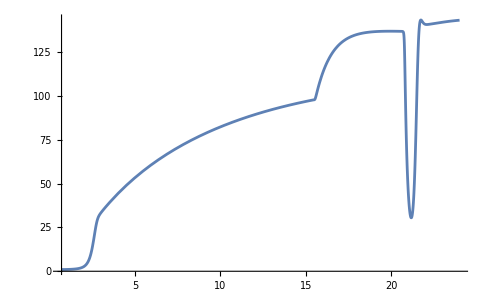

```mathematica
Plot[Evaluate[Sum[x[i][t],{i,1,500}]/.soln500beta],{t,0.71,24},PlotRange->All]
```

Substrate concentration (μM C)

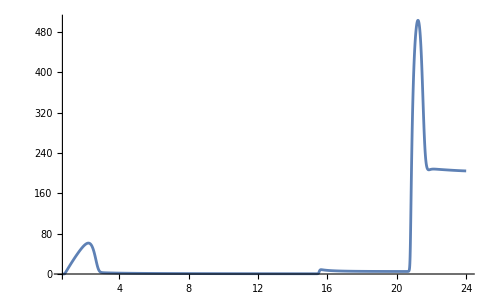

```mathematica
Plot[Evaluate[s[t]/.soln500beta],{t,0.71,24},PlotRange->All]
```

Export the ASVs for the beta distribution simulation

```mathematica
Export["betaASVs.csv",Prepend[betaASVs,Flatten[{"ASVs",times}]]]
```

betaASVsB.csv

```mathematica
Export["betaASVsRelative.csv",Prepend[betaASVsRel,Flatten[{"ASVs",times}]]]
```

betaASVsRelative.csv

### Beta Distribution #2

```mathematica
betaSampleB=RandomVariate[BetaDistribution[α,β]/.params,500];
```

```mathematica
betaSampleB
```

{0.0583944,0.0171301,0.381871,0.0812716,0.0229149,0.0148772,0.0027823,0.165252,0.027033,0.178466,0.0344182,0.0396093,0.115233,0.0639945,0.139469,0.0593945,0.0586851,0.00888969,0.100853,0.0197604,0.114058,0.262048,0.103457,0.00811094,0.149631,0.0846868,0.0225225,0.0122804,0.0224947,0.00552387,0.0356855,0.291925,0.128006,0.0202287,0.137416,0.0230738,0.147483,0.0353588,0.00411561,0.0093462,0.086562,0.0639693,0.0749235,0.120406,0.0254157,0.0175486,0.0400621,0.0605474,0.0852225,0.0297624,0.210045,0.00113546,0.134457,0.0257904,0.118791,0.112617,0.0886975,0.0168652,0.182095,0.017579,0.105206,0.000224001,0.0192672,0.024936,0.13402,0.247295,0.0907659,0.117818,0.00620472,0.0510281,0.0519454,0.00661866,0.171103,0.0296955,0.0216998,0.0284744,0.0997175,0.0590732,0.0202071,0.0216055,0.0286797,0.0441588,0.0212491,0.0384482,0.0211827,0.00309518,0.0281527,0.218307,0.0678666,0.0218255,0.02634,0.0105483,0.0504281,0.02004,0.112919,0.0213017,0.0224019,0.059374,0.0499963,0.126043,0.135189,0.00664061,0.186485,0.0726298,0.412763,0.0586142,0.121482,0.26987,0.0470519,0.0634042,0.183999,0.0778283,0.0250448,0.134652,0.230187,0.0708705,0.0164664,0.225201,0.0731088,0.0140745,0.1057,0.00922385,0.0942447,0.0881882,0.054496,0.0237379,0.00941319,0.24414,0.0831622,0.0460891,0.339567,0.0898508,0.0115611,0.0450398,0.258264,0.00184572,0.195883,0.0292549,0.220388,0.0730396,0.0237729,0.0393197,0.0533959,0.0445692,0.0199051,0.115595,0.0723454,0.0864271,0.0815738,0.0576542,0.0212123,0.0117145,0.0148381,0.0682846,0.0906712,0.33388,0.0448718,0.00691282,0.098685,0.101789,0.137467,0.0511054,0.108436,0.0639019,0.0433863,0.218817,0.0203423,0.00228289,0.0775715,0.00900855,0.0498861,0.126086,0.00175313,0.0154016,0.0849711,0.131824,0.0813538,0.119859,0.147283,0.0523358,0.0202968,0.083392,0.150189,0.113205,0.00492985,0.0301504,0.0916147,0.072473,0.0246381,0.150123,0.0475754,0.197253,0.0354323,0.178867,0.094709,0.0156339,0.0572878,0.0211496,0.00782521,0.0570054,0.0181591,0.106711,0.0523614,0.00486259,0.0464349,0.107514,0.136208,0.23033,0.052111,0.0481674,0.0349363,0.0799184,0.256506,0.0567056,0.0418038,0.0275866,0.235731,0.173988,0.0307257,0.0160567,0.136389,0.056971,0.0823094,0.0719874,0.00187057,0.011828,0.405636,0.14528,0.0316831,0.0310198,0.0607111,0.058451,0.244327,0.308429,0.00255127,0.0229202,0.115149,0.111702,0.0874443,0.0446643,0.00605347,0.138156,0.0357824,0.121978,0.0489567,0.0417871,0.0103107,0.00358518,0.0883703,0.107655,0.132933,0.224269,0.0349268,0.0643251,0.0699661,0.0668568,0.00622942,0.000737282,0.000424857,0.186782,0.0530761,0.0868617,0.0385015,0.0179731,0.0103378,0.224208,0.0132655,0.153935,0.0709558,0.0709213,0.0112698,0.0870923,0.0931588,0.01135,0.139592,0.0206631,0.0646883,0.00736773,0.0581262,0.123384,0.0758273,0.0961996,0.0778232,0.00289537,0.0385326,0.0120332,0.0869153,0.0910202,0.185952,0.0280852,0.0257136,0.176761,0.196349,0.13039,0.0198338,0.0957252,0.089112,0.0957204,0.0760564,0.224045,0.0701113,0.0279579,0.190841,0.0226704,0.120098,0.0671465,0.10011,0.0213977,0.090421,0.0681566,0.123702,0.0789709,0.12981,0.0497205,0.0598461,0.118623,0.0718946,0.0863326,0.00233737,0.00160146,0.0135828,0.341332,0.0122027,0.117454,0.15925,0.0689701,0.0995839,0.0263559,0.0890027,0.191147,0.106446,0.0483556,0.0386708,0.131825,0.234495,0.0884102,0.0508753,0.0502562,0.0123126,0.0434465,0.0646635,0.0222409,0.0750694,0.00597357,0.0347577,0.00533747,0.0260613,0.158275,0.0702473,0.0472794,0.0412123,0.0994364,0.0280829,0.0318009,0.022244,0.0568598,0.0321106,0.110441,0.0401906,0.0237711,0.156436,0.233353,0.25206,0.167414,0.146098,0.00555439,0.0106227,0.0596042,0.0512247,0.0542189,0.0594385,0.0390768,0.0556996,0.0221888,0.104254,0.109729,0.039031,0.0365892,0.0696376,0.075258,0.175538,0.021497,0.0663075,0.250452,0.0210677,0.0982863,0.00896369,0.00488553,0.00334905,0.00960463,0.0317858,0.0543648,0.0277315,0.0496629,0.0694669,0.029148,0.0964774,0.0193391,0.0263271,0.0306125,0.00116564,0.0970202,0.0106669,0.0643945,0.126967,0.0156591,0.0599526,0.00986196,0.124876,0.0260717,0.0125408,0.00318176,0.003397,0.0426337,0.023745,0.124129,0.102112,0.0128335,0.20915,0.0218563,0.0851829,0.0540526,0.112444,0.00238781,0.0921643,0.0987943,0.0113156,0.218236,0.0270119,0.108167,0.0149944,0.160723,0.0199667,0.0780551,0.15162,0.00587372,0.039589,0.0130988,0.045504,0.0826082,0.00256389,0.0453483,0.190339,0.00683566,0.0136591,0.00444686,0.00560188,0.130449,0.0268039,0.171961,0.107748,0.170919,0.211697,0.0238301,0.0906513,0.00543879,0.0635304,0.0664649,0.0450264,0.197441,0.0224164,0.0766163,0.0371346,0.00276182,0.0595466,0.10589,0.0229868,0.141696,0.0191797,0.0497505,0.069877,0.0986225,0.224354,0.115106,0.0568503,0.0792988,0.0137821,0.0549303,0.0245668,0.00842486,0.127183,0.0160149,0.0836651,0.0515824,0.003268,0.0997625,0.0438432,0.0331915,0.0258643,0.0242351,0.0589948,0.0611394,0.178447,0.101473,0.0634012,0.0201695,0.067258,0.13395,0.075732,0.165791}

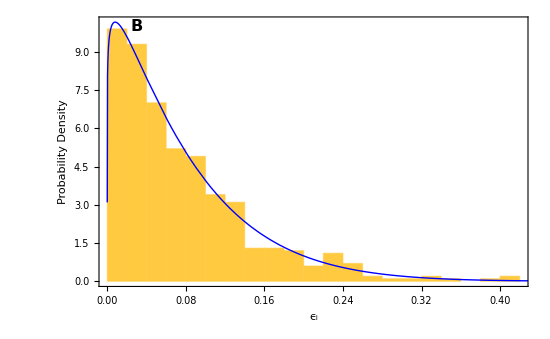

```mathematica
betaDistributionPlot=Show[Histogram[betaSampleB,Automatic,"ProbabilityDensity", Frame->{{True,False},{True,False}},FrameLabel->{{"Probability Density",""},{"ϵ_i",""}},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16],{0.03,10}]},ImageSize->550],Plot[PDF[BetaDistribution[α,β]/.params,x],{x,0,1},PlotStyle->{Thick,Blue},PlotRange->{{0,0.7},All}]]
```

```mathematica
soln500betaB=solveODEs[0.71,24,params,betaSampleB];
```

```mathematica
Rasterize[xiBetaPlotB=ListLinePlot[Evaluate[Table[{t,x[i][t]},{i,1,500},{t,0.71,24,0.1}]/.soln500betaB],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","x_i(t) concentration (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->18,FontColor->Black},PlotStyle->Thick,FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16],{2,70}]},ImageSize->550]]
```

-Graphics-

```mathematica
times={0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5}; 
betaASVsB=Prepend[Evaluate[Table[Table[x[i][t],{i,1,500}]/.soln500betaB/.t->times⟦j⟧,{j,1,Length[times]}]],Evaluate[Table["ASV_"<>ToString[i],{i,500}]]]ᵀ;
betaASVsRelB=Prepend[Table[100betaASVsB⟦1;;,i⟧/Total[betaASVsB⟦1;;,i⟧],{i,2,Dimensions[betaASVsB]⟦2⟧}],betaASVsB⟦1;;,1⟧]ᵀ;
```

```mathematica
asvMinAbunRel=0.1;
asvBetaMinB=Chop[N[betaASVsRelB],asvMinAbunRel]; (* this sets any ASV that is < asvMinAbunRel to 0 *)
```

```mathematica
Rasterize[xiBarBetaPlotB=xiBarChart[asvBetaMinB⟦1;;,2;;⟧ᵀ,{{0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5},Table["",{14}]},{1,5,6,9,10,14},"B"]]
```

-Graphics-

```mathematica
Export["xiBarBetaPlotB.svg",xiBarBetaPlotB]
```

xiBarBetaPlotB.svg

```mathematica
Export["betaASVsRelativeB.csv",Prepend[betaASVsRelB,Flatten[{"ASVs",times}]]]
```

betaASVsRelativeB.csv

```mathematica
Export["betaASVsB.csv",Prepend[betaASVsB,Flatten[{"ASVs",times}]]]
```

betaASVsB.csv

## Simulation comparison to observed pO_2 and DO

Plot the simulated vs observed and export fig.

```mathematica
Rasterize[pO2andDOFig=GraphicsRow[{Show[ListLinePlot[o2Data,PlotRange->{{0,23.6},All},PlotStyle->{Black,Gray},PlotLegends->Placed[LineLegend[{Black,Gray,Blue,Red},{"MC 1","MC 2","Uniform","Beta"}],Center],Epilog->{Text[Style["A",Bold,FontFamily->"Arial",FontSize->16,FontColor->Black],{23,21.1}]}],Plot[Evaluate[100pO2[t]/.soln500beta],{t,0.71,25},PlotStyle->Red,PlotRange->All],Plot[Evaluate[100pO2[t]/.soln500],{t,0.71,24},PlotStyle->Blue,PlotRange->All],Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","pO_2 (%)"},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},PlotRange->{{0,23.6},{20,21.1}},PlotLegends->Placed[LineLegend[{Black,Gray,Blue,Red},{"MC 1","MC 2","Uniform","Beta"}],Center]],
Show[ListLinePlot[doData,PlotRange->{{0,23.6},All},PlotStyle->{Black,Gray},PlotLegends->Placed[LineLegend[{Black,Gray,Blue,Red},{"MC 1","MC 2","Uniform","Beta"}],Center],Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16,FontColor->Black],{23,270}]}],Plot[Evaluate[o2[t]/.soln500beta],{t,0.71,24},PlotStyle->Red,PlotRange->All],Plot[Evaluate[o2[t]/.soln500],{t,0.71,24},PlotStyle->Blue,PlotRange->All],Frame->{{True,False},{True,False}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},FrameLabel->{"Time (d)","DO (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},PlotRange->{{0,23.6},{0,275}}]},ImageSize->1024]]
```

-Graphics-

```mathematica
Export["pO2andDOFig.svg",pO2andDOFig]
```

pO2andDOFig.svg

```mathematica
Rasterize[pO2Fig=Show[ListLinePlot[o2Data,PlotRange->{{0,23.6},All},PlotStyle->{Black,Gray},PlotLegends->Placed[LineLegend[{Black,Gray,Blue,Red},{"MC 1","MC 2","Uniform","Beta"}],Center],Epilog->{Text[Style["A",Bold,FontFamily->"Arial",FontSize->16,FontColor->Black],{23,21.1}]}],Plot[Evaluate[100pO2[t]/.soln500beta],{t,0.71,25},PlotStyle->Red,PlotRange->All],Plot[Evaluate[100pO2[t]/.soln500],{t,0.71,24},PlotStyle->Blue,PlotRange->All],Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","pO_2 (%)"},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},PlotRange->{{0,23.6},{20,21.1}},PlotLegends->Placed[LineLegend[{Black,Gray,Blue,Red},{"MC 1","MC 2","Uniform","Beta"}],Center],ImageSize->550]]
```

-Graphics-

```mathematica
Export["pO2Fig.svg",pO2Fig]
```

pO2Fig.svg

```mathematica
Rasterize[DOFig=Show[ListLinePlot[doData,PlotRange->{{0,23.6},All},PlotStyle->{Black,Gray},PlotLegends->Placed[LineLegend[{Black,Gray,Blue,Red},{"MC 1","MC 2","Uniform","Beta"}],Center],Epilog->{Text[Style["B",Bold,FontFamily->"Arial",FontSize->16,FontColor->Black],{23,270}]}],Plot[Evaluate[o2[t]/.soln500beta],{t,0.71,24},PlotStyle->Red,PlotRange->All],Plot[Evaluate[o2[t]/.soln500],{t,0.71,24},PlotStyle->Blue,PlotRange->All],Frame->{{True,False},{True,False}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},FrameLabel->{"Time (d)","DO (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},PlotRange->{{0,23.6},{0,275}},ImageSize->550]]
```

-Graphics-

```mathematica
Export["DOFig.svg",DOFig]
```

DOFig.svg

### Total simulated bacterial concentrations for both distributions

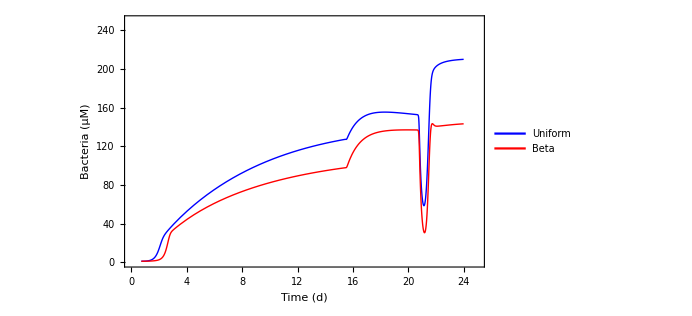

```mathematica
modelBacteriaConcentrationFig=Plot[{Evaluate[Sum[x[i][t],{i,1,500}]/.soln500],Evaluate[Sum[x[i][t],{i,1,500}]/.soln500beta]},{t,0.71,24},Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","Bacteria (μM)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},PlotRange->{{0,25},{0,250}},ImageSize->512,PlotStyle->{{Thick,Blue},{Thick,Red}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},PlotLegends->Placed[LineLegend[{Blue,Red},{"Uniform","Beta"}],{0.25,0.8}]]
```

```mathematica
Export["modelBacteriaConcentrationFig.svg",modelBacteriaConcentrationFig]
```

modelBacteriaConcentrationFig.svg

Import  bacterial cell counts

```mathematica
counts=Import["..\\Data\\BacterialCellCounts.csv"];
```

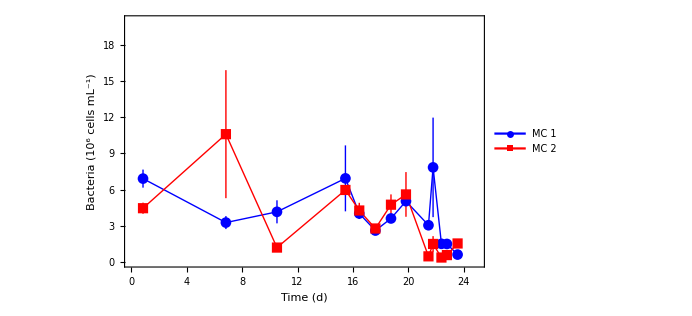

```mathematica
bacterialCounts=ListLinePlot[{counts⟦2;;,{1,2,3}⟧/.{x_,y_,z_}->{x,Around[10^-6 y,10^-6 z]},counts⟦2;;,{1,4,5}⟧/.{x_,y_,z_}->{x,Around[10^-6 y,10^-6 z]}},PlotMarkers->Automatic,Frame->{{True,False},{True,False}},FrameLabel->{"Time (d)","Bacteria (10^6 cells mL^-1)"},LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},PlotRange->{{0,25},{0,20}},ImageSize->512,PlotStyle->{{Thick,Blue},{Thick,Red}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},PlotLegends->Placed[LineLegend[{Blue,Red},{"MC 1","MC 2"}],{0.1,0.9}]]
```

```mathematica
Export["BacterialCounts.svg",bacterialCounts]
```

BacterialCounts.svg

## Observed ASV Data Plots

Import  all of the ASV data for MC1 and MC2, including taxa names and ASV data for Siders Pond which is in the file Table_S1_ASVs.csv in the Data subdirectory. Drop the header.

### Data and plot function

```mathematica
asvData=Drop[Import["..\\Data\\TableS1_ASVs.csv"],1];
```

```mathematica
Dimensions[asvData]
```

{1420,34}

Get  the  ASV taxon names

```mathematica
taxaNames=asvData⟦;;,{29,30,31,32,33,34}⟧;
```

Add  Siders  ASV  data  as  time  “Siders”  to  each  dataset and specify when samples were collected in days, which are slightly different for each MC.

```mathematica
timesMC1={"Siders",0.8, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5}; 
timesMC2={"Siders",0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,23.5}; 
timesMC12={"Siders",0.8, 6.8, 9.5, 10.5, 15.5, 16.5, 17.6, 18.8, 19.8,21.5,21.8,22.4,22.8,23.5};
```

```mathematica
asvMC1=Table[0,Dimensions[asvData]⟦1⟧,Length[timesMC12]+1]; (* initialize these to 0 *)
asvMC2=Table[0,Dimensions[asvData]⟦1⟧,Length[timesMC12]+1];
```

Copy  in  the  asvData, but add in Siders’ ASVs and keep columns 0 for where samples did not sequence.

```mathematica
asvMC1⟦;;,Flatten[{1,2,3,Range[6,16]}]⟧=asvData⟦;;,Range[1,14]⟧;
asvMC2⟦;;,Flatten[{Range[1,14],16}]⟧=asvData⟦;;,Flatten[{1,2,Range[15,27]}]⟧;
```

Define function to name and ASV based on columns in taxaNames above

```mathematica
nameMake[n1_String,n2_String]:=n1<>" "<>n2
```

Define  function for generating bar charts with a percentage cutoff. This  version  of plotASVobs sets ASVs with relative abundances less than minPer to zero instead of removing them. That way, ASV color indexes stay the same. maxLedgend specifies how many of the top ASV taxon names to display, and colorIndex is based on the Mathematica’s Indexed Color Palette Collections

```mathematica
plotASVobs[asvData_,timePts_List,minPer_,maxLedgend_,colorIndex_,dBars_List,fig_]:=Module[{asvDataRel,asvDataRelmin,tf,colors},
(*Relative abundance of an ASV in each sample time, gen in percentage*)
asvDataRel=Prepend[Table[100asvData⟦;;,i⟧/If[Total[asvData⟦;;,i⟧]!=0,Total[asvData⟦;;,i⟧],1],{i,2,Dimensions[asvData]⟦2⟧}],asvData⟦;;,1⟧]ᵀ;
(*Any ASV less than minPer is set to zero. Note, Chop only works on reals, not integers or rational numbers*)
asvDataRelmin=Chop[N[asvDataRel],minPer];
(*Get a vector of colors based on colorIndex and add it as the first column *)
colors=Table[ColorData[colorIndex][i],{i,Length[asvData]}];
asvDataRelmin=Join[Partition[colors,1],asvDataRelmin,2];
(* sort asvDataRelmin so the largest are first *)
asvDataRelmin=ReverseSortBy[asvDataRelmin,Max[#⟦3;;⟧]&];
tf[p_]:=TableForm[Partition[Flatten[p],UpTo[10]],TableSpacing->{1,1}];
TableForm[{BarChart[asvDataRelmin⟦;;,3;;⟧ᵀ,ChartLayout->"Stacked",ChartLabels->{timePts,Table["",{Length[asvDataRelmin]}]},PlotRange->{{0.5,Dimensions[asvDataRelmin]⟦2⟧-1.5},{0,100}}, LabelStyle->{Bold,FontFamily->"Arial",FontSize->16,FontColor->Black},ChartStyle->asvDataRelmin⟦;;,1⟧,FrameLabel->{"Time (d)","ASV Rel. Abundance (%)"},Frame->{{True,False},{True,False}},FrameStyle->{{Directive[Thick,Black],None},{Directive[Thick,Black],None}},ImagePadding->{{All,All},{All,30}},ImageSize->550,Epilog->{Text[Style[fig,Bold,FontFamily->"Arial",FontSize->16],{1,105}],Thick,Text[Style["D = 0.1 d^-1",Bold,14],{(dBars⟦1⟧+dBars⟦2⟧)/2,105}],Line[{{dBars⟦1⟧-0.3,101},{dBars⟦2⟧+0.3,101}}],Text[Style["D = 1.0 d^-1",Bold,14],{(dBars⟦3⟧+dBars⟦4⟧)/2,105}],Text[Style["D = 10. d^-1",Bold,14],{(dBars⟦5⟧+dBars⟦6⟧)/2,105}],Line[{{dBars⟦3⟧-0.3,101},{dBars⟦4⟧+0.3,101}}],Line[{{dBars⟦5⟧-0.3,101},{dBars⟦6⟧+0.3,101}}]}],
SwatchLegend[asvDataRelmin⟦;;maxLedgend,1⟧,asvDataRelmin⟦;;maxLedgend,2⟧,LegendMarkerSize->10,LabelStyle->{FontSize->8},LegendLayout->tf]}]
];
```

Plot  with  names from Family

```mathematica
familyMC1=asvMC1;familyMC1⟦;;,1⟧=Thread[nameMake[taxaNames⟦;;,5⟧,asvMC1⟦;;,1⟧]];
familyMC2=asvMC2;familyMC2⟦;;,1⟧=Thread[nameMake[taxaNames⟦;;,5⟧,asvMC2⟦;;,1⟧]];
```

### Barcharts

Plot  ASVs who’s relative abundance > 0.1%

```mathematica
Rasterize[mc1family=plotASVobs[familyMC1,timesMC12,0.1,10,24,{2,6,7,10,11,15},"A"]]
```

-Graphics-

```mathematica
Rasterize[mc2family=plotASVobs[familyMC2,timesMC12,0.1,10,24,{2,6,7,10,11,15},"B"]]
```

-Graphics-

```mathematica
Export["familyMC1_24.svg",mc1family];
Export["familyMC2_24.svg",mc2family];
```

Generate  a  legend based on the top maxLedgend based on both MCs

```mathematica
legendASVobs[asvData_,minPer_,maxLedgend_,colorIndex_,fontSize_]:=Module[{asvDataRel,asvDataRelmin,tf,colors},
(*Relative abundance of an ASV in each sample time, gen in percentage*)
asvDataRel=Prepend[Table[100asvData⟦;;,i⟧/If[Total[asvData⟦;;,i⟧]!=0,Total[asvData⟦;;,i⟧],1],{i,2,Dimensions[asvData]⟦2⟧}],asvData⟦;;,1⟧]ᵀ;
(*Any ASV less than minPer is set to zero. Note, Chop only works on reals, not integers or rational numbers*)
asvDataRelmin=Chop[N[asvDataRel],minPer];
(*Get a vector of colors based on colorIndex and add it as the first column *)
colors=Table[ColorData[colorIndex][i],{i,Length[asvData]}];
asvDataRelmin=Join[Partition[colors,1],asvDataRelmin,2];
(* sort asvDataRelmin so the largest are first *)
asvDataRelmin=ReverseSortBy[asvDataRelmin,Max[#⟦3;;⟧]&];
tf[p_]:=TableForm[Partition[Flatten[p],UpTo[10]],TableSpacing->{1,1}];
SwatchLegend[asvDataRelmin⟦;;maxLedgend,1⟧,asvDataRelmin⟦;;maxLedgend,2⟧,LegendMarkerSize->10,LabelStyle->{FontSize->fontSize},LegendLayout->tf]
]
```

Top  ASVs  for  both  MCs

```mathematica
legendFamilyTop30=legendASVobs[Join[familyMC1,familyMC2⟦;;,Range[3,16]⟧,2],0.1,30,24,10]
```

```mathematica
Export["legendFamilyTop30.svg",legendFamilyTop30]
```

legendFamilyTop30.svg

Plot  with  names from Order

```mathematica
orderMC1=asvMC1;orderMC1⟦;;,1⟧=Thread[nameMake[taxaNames⟦;;,4⟧,asvMC1⟦;;,1⟧]];
orderMC2=asvMC2;orderMC2⟦;;,1⟧=Thread[nameMake[taxaNames⟦;;,4⟧,asvMC2⟦;;,1⟧]];
```

Plot  ASVs who’s relative abundance > 0.1%

```mathematica
Export["orderMC1_24b.svg",mc1Order];
Export["orderMC2_24b.svg",mc2Order];
```

## Conclusions

We see a decrease in α diversity with increasing dilution rate that matches the chemostat data only if the community maximum specific growth rate is skewed like the beta distribution; that is, the natural community appears to be skewed towards gleaners (oligotrophs) over opportunists (copiotrophs).